```mathematica
normalOrderingRules =  xpOpString[a___, p, x, b___] -> xpOpString[a, x, p, b] - ⅈ xpOpString[a, b];
mulRules = {xpOpString[a___] . xpOpString[b___] -> xpOpString[a, b], 
c_ . xpOpString[a___] /; NumberQ[c] -> c xpOpString[a],
xpOpString[a___] . c_ /; NumberQ[c] -> c xpOpString[a],
a_ . b_ /; NumberQ[a] && NumberQ[b] -> a b};
```

```mathematica
xntimes[n_] := xpOpString @@ ConstantArray[x, n];
pntimes[n_] := xpOpString @@ ConstantArray[p, n];
xntimes[0] := 1;
pntimes[0] := 1;
xpNormalOrderedOp[xpower_, ppower_] := xntimes[xpower] . pntimes[ppower] /. mulRules;
```

```mathematica
basis = Flatten[Table[xpNormalOrderedOp[xpower, ppower], {xpower, 0, 5}, {ppower, 0, 5}]];
basislen = Length[basis];
```

```mathematica
M = Table[basis⟦i⟧ . basis⟦j⟧ //. mulRules //. normalOrderingRules // Simplify, {i, 1, basislen}, {j, 1, basislen}]
```

{{1,xpOpString[p],xpOpString[p,p],xpOpString[p,p,p],xpOpString[p,p,p,p],xpOpString[p,p,p,p,p],xpOpString[x],xpOpString[x,p],20,xpOpString[x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,p,p,p,p,p],xpOpString[x,x,x,x,x],xpOpString[x,x,x,x,x,p],xpOpString[x,x,x,x,x,p,p],xpOpString[x,x,x,x,x,p,p,p],xpOpString[x,x,x,x,x,p,p,p,p],xpOpString[x,x,x,x,x,p,p,p,p,p]},34,{1}}
 |  |  |  |

```mathematica
basis⟦27⟧ . basis⟦16⟧ //. mulRules //. normalOrderingRules // Simplify
```

-2 xpOpString[x,x,x,x,p,p,p]-4 ⅈ xpOpString[x,x,x,x,x,p,p,p,p]+xpOpString[x,x,x,x,x,x,p,p,p,p,p]

```mathematica
M⟦27, 16⟧
```

-2 xpOpString[x,x,x,x,p,p,p]-4 ⅈ xpOpString[x,x,x,x,x,p,p,p,p]+xpOpString[x,x,x,x,x,x,p,p,p,p,p]

含有复数的linear SDP问题

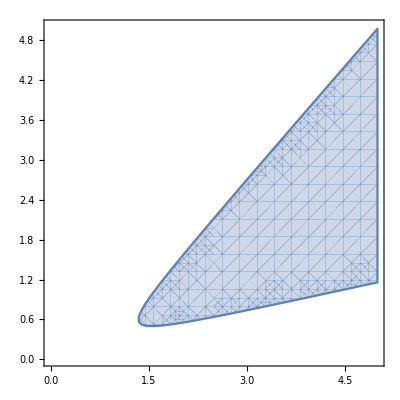

```mathematica
RegionPlot[AllTrue[Eigenvalues[({{x1, x1 + ⅈ x2, x2 + 0.5}, {x1 - ⅈ x2, 5 x2, 0}, {x2 + 0.5, 0, x1 + x2}})], # ≥ 0 &], {x1, 0, 5}, {x2, 0, 5}]
```

```mathematica
FindMinimum[{2 x1 + 3 x2, AllTrue[Eigenvalues[({{x1, x1 + ⅈ x2, x2 + 0.5}, {x1 - ⅈ x2, 5 x2, 0}, {x2 + 0.5, 0, x1 + x2}})], # ≥ 0 &]}, {x1, 5}, {x2, 5}]
```

{4.35069,{x1→1.38081,x2→0.529692}}

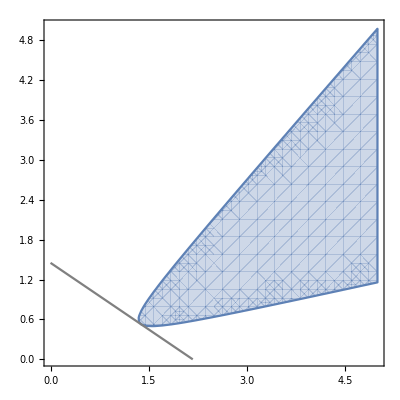

```mathematica
constraints = AllTrue[Eigenvalues[({{x1, x1 + ⅈ x2, x2 + 0.5}, {x1 - ⅈ x2, 5 x2, 0}, {x2 + 0.5, 0, x1 + x2}})], # ≥ 0 &];
feasible = RegionPlot[constraints, {x1, 0, 5}, {x2, 0, 5}];
H = 2 x1 + 3 x2;
H0 = FindMinimum[{2 x1 + 3 x2, constraints}, {x1, 5}, {x2, 5}]⟦1⟧;
Show[{feasible, ContourPlot[H == H0, {x1, 0, 5}, {x2, 0, 5}, ContourStyle->Gray]}]
```

```mathematica
FindMinimum[{2 x1 + 3 x2, constraints}, {x1, 5}, {x2, 5}]⟦2⟧
```

{x1→1.38081,x2→0.529692}

```mathematica
H0
```

4.35069